```mathematica
"Skin2`QuaSK`"//Needs
```

```mathematica
(*Q – нормированный на 1 кватернион, который задет врещение на φ относительно произвольной оси с координатами {nx,ny,nz}. 
Радиальный спин-кик может в этих терминах задаваться как Q[φ,1,0,0].
Так же (для удобства) задаем кватернион q, который задает вращение относильно накланенной оси на угол ψ. 
При этом продольная компонента локальной инваринатой оси равна нулю*)
```

```mathematica
Q[φ_,nx_,ny_,nz_]=ToQua[1,φ,{nx,ny,nz}]
q[φ_,ψ_]=ToQua[1,φ,{Sin[ψ],Cos[ψ],0}]
```

```mathematica
a1=q[π/3,π/3]
Rotation[a1]
a1**a1
Rotation[a1**a1]
```

Qua[(√3)/2,(√3)/4,1/4,0]

{Angle→π/3,Axis→{(√3)/4,1/4,0}}

Qua[1/2,3/4,(√3)/4,0]

{Angle→(2 π)/3,Axis→{3/4,(√3)/4,0}}

```mathematica
Qua[Cos[φ/2],(Sin[φ/2] Sin[ψ])/(√(Cos[ψ]^2+Sin[ψ]^2)),(Cos[ψ] Sin[φ/2])/(√(Cos[ψ]^2+Sin[ψ]^2)),0]
```

Qua[Cos[φ/2],(Sin[φ/2] Sin[ψ])/(√(Cos[ψ]^2+Sin[ψ]^2)),(Cos[ψ] Sin[φ/2])/(√(Cos[ψ]^2+Sin[ψ]^2)),0]

```mathematica
Qua[Cos[φ/2],(Sin[φ/2] Sin[ψ])/(√(Cos[ψ]^2+Sin[ψ]^2)),(Cos[ψ] Sin[φ/2])/(√(Cos[ψ]^2+Sin[ψ]^2)),0]
```

Qua[Cos[φ/2],(Sin[φ/2] Sin[ψ])/(√(Cos[ψ]^2+Sin[ψ]^2)),(Cos[ψ] Sin[φ/2])/(√(Cos[ψ]^2+Sin[ψ]^2)),0]

```mathematica
(*показываем эквавалентность заданных кватернионов*)
```

```mathematica
Q1=Q[π/3,Sin[π/3],Cos[π/3],0]
q1=q[π/3,π/3]
```

Qua[(√3)/2,(√3)/4,1/4,0]

Qua[(√3)/2,(√3)/4,1/4,0]

```mathematica
(*показываем угол заданного вращения и ось, относительно которой происходит поворот*)
```

```mathematica
Rotation[q1]
Rotation[Q1]
```

{Angle→π/3,Axis→{(√3)/4,1/4,0}}

```mathematica
{Angle->π/3,Axis->{(√3)/4,1/4,0}}
```

```mathematica
(*Рассмотрим случай с наклоненными магнитами*)
```

```mathematica
q1**q1
Rotation[q1**q1]
```

Qua[1/2,3/4,(√3)/4,0]

{Angle→(2 π)/3,Axis→{3/4,(√3)/4,0}}

```mathematica
(*Случайное число из распределения c мат.ожидаением 0 и стандартным отклонением 1*)
```

```mathematica
RandomVariate[NormalDistribution[0,10^-4]]
```

-0.0000861685

-0.012535

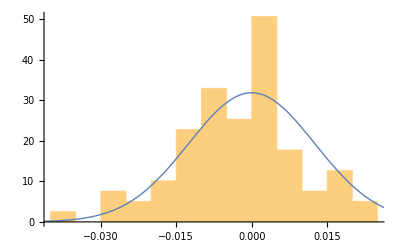

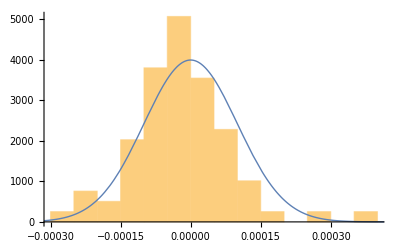

```mathematica
(*Задание углов Θ–повороты вокруг оси, Ψ–наклон оси относительно продольной оси (движение в x-y плоскости) в радианах
через нормально распеделение.
Важно правильно определить пределы для обоих распределений*)
γ=1.14;G=-0.14;
Subscript[N, dip]=80;Subscript[ρ, hist]=10; Subscript[Ψ, sigma]=10^-4;Subscript[Θ, sigma]=γ*G*(2π)/Subscript[N, dip]
(*Формируем набор из 80 случайных чисел из распределения c мат.ожидаением 0 и стандартным отклонением 10^-4 *)
Θ=RandomVariate[NormalDistribution[0,Abs[Subscript[Θ, sigma]]],Subscript[N, dip]-1];
Ψ=RandomVariate[NormalDistribution[0,Subscript[Ψ, sigma]],Subscript[N, dip]-1];
(*Построение гистограм*)
Show[Histogram[Θ,10,"ProbabilityDensity"],Plot[PDF[NormalDistribution[0,0.012534954687823273],x],{x,-0.05,0.05},PlotStyle->Thick]]
Show[Histogram[Ψ,10,"ProbabilityDensity"],Plot[PDF[NormalDistribution[0,10^-4],x],{x,-0.0005,0.0005},PlotStyle->Thick]]
```

```mathematica
Ψ
AppendTo[Ψ,-∑_(i=1)^(Subscript[N, dip]-1) Ψ[[i]]]
∑_(i=1)^Subscript[N, dip] Ψ[[i]]
Θ
AppendTo[Θ,-∑_(i=1)^(Subscript[N, dip]-1) Θ[[i]]]
∑_(i=1)^Subscript[N, dip] Θ[[i]]
```

{0.0000395688,-0.000134537,-0.0000627899,0.000142614,0.000081465,-0.0000369363,-0.000122568,-0.0000457883,0.0000922298,-0.000179842,-0.0000187923,-0.0000108964,-0.000161261,0.0000830034,8.88886×10^-6,-0.0000135314,0.0000325747,-0.0000980591,0.000043502,-0.0000469565,-9.4568×10^-6,0.0000565527,0.0000363269,-0.000017283,0.0000501557,-0.000140271,-6.51739×10^-6,-0.0000961792,-0.0000851992,-0.0000757992,0.00012423,0.0000426833,0.0000426695,-0.0000938433,-6.08726×10^-6,-0.000084821,-0.0000565727,0.0000499587,0.0000249104,-0.0000947567,0.0000996948,-0.000213554,-0.0000503639,0.00036566,-2.37605×10^-7,-0.000124025,-0.0000140732,-0.0000533833,-0.0000700915,0.000130722,0.0000150046,-0.0000347349,-0.000258577,0.00027658,-0.000206527,0.0000127332,0.000143917,-0.00014315,-0.0000591484,0.0000384218,-0.0000359403,0.0000869744,0.0000420775,0.0000915813,-0.0000203383,0.0000188153,-1.27478×10^-6,0.000163603,0.0000848681,-0.000206827,-0.000135124,-0.0000198174,-0.0000285799,-0.000129682,-0.0000783429,-0.000102436,-0.000049329,-0.0000479932,-0.0000875836}

{0.0000395688,-0.000134537,-0.0000627899,0.000142614,0.000081465,-0.0000369363,-0.000122568,-0.0000457883,0.0000922298,-0.000179842,-0.0000187923,-0.0000108964,-0.000161261,0.0000830034,8.88886×10^-6,-0.0000135314,0.0000325747,-0.0000980591,0.000043502,-0.0000469565,-9.4568×10^-6,0.0000565527,0.0000363269,-0.000017283,0.0000501557,-0.000140271,-6.51739×10^-6,-0.0000961792,-0.0000851992,-0.0000757992,0.00012423,0.0000426833,0.0000426695,-0.0000938433,-6.08726×10^-6,-0.000084821,-0.0000565727,0.0000499587,0.0000249104,-0.0000947567,0.0000996948,-0.000213554,-0.0000503639,0.00036566,-2.37605×10^-7,-0.000124025,-0.0000140732,-0.0000533833,-0.0000700915,0.000130722,0.0000150046,-0.0000347349,-0.000258577,0.00027658,-0.000206527,0.0000127332,0.000143917,-0.00014315,-0.0000591484,0.0000384218,-0.0000359403,0.0000869744,0.0000420775,0.0000915813,-0.0000203383,0.0000188153,-1.27478×10^-6,0.000163603,0.0000848681,-0.000206827,-0.000135124,-0.0000198174,-0.0000285799,-0.000129682,-0.0000783429,-0.000102436,-0.000049329,-0.0000479932,-0.0000875836,0.00134789}

0.

{0.00380589,0.00740689,0.0174916,-0.0221915,-0.00542241,-0.00818222,-0.00714744,-0.0084832,-0.00135141,-0.0368392,-0.00434606,0.00304744,0.000690886,0.000472727,-0.011047,0.0160637,-0.0165489,-0.017419,-0.0134247,-0.00309457,0.000651611,-0.0147396,0.0247211,0.00221287,-0.0140082,0.00124455,0.00169367,-0.00514155,0.0178625,0.0074728,-0.00396378,0.000896295,-0.00772583,-0.0295441,-0.00554396,-0.0108955,0.0079636,-0.00294809,-0.00804454,-0.0000583768,0.00816929,-0.0206293,0.0120681,-0.0129959,-0.0258823,-0.00948666,0.00144029,0.00415332,-0.00684622,-0.00605996,-0.00603681,-0.0117936,0.0077657,0.0215919,-0.00646674,-0.0156935,-0.00139423,-0.000375322,0.00162548,-0.0184506,0.00432987,0.00225567,0.00893467,0.0143348,0.00321893,-0.0112444,0.000748821,0.00155518,-0.00335052,0.00374679,0.00598614,0.0025509,0.0144808,-0.0262301,0.0182937,0.0185558,0.000969652,-0.00159024,-0.0129999}

{0.00380589,0.00740689,0.0174916,-0.0221915,-0.00542241,-0.00818222,-0.00714744,-0.0084832,-0.00135141,-0.0368392,-0.00434606,0.00304744,0.000690886,0.000472727,-0.011047,0.0160637,-0.0165489,-0.017419,-0.0134247,-0.00309457,0.000651611,-0.0147396,0.0247211,0.00221287,-0.0140082,0.00124455,0.00169367,-0.00514155,0.0178625,0.0074728,-0.00396378,0.000896295,-0.00772583,-0.0295441,-0.00554396,-0.0108955,0.0079636,-0.00294809,-0.00804454,-0.0000583768,0.00816929,-0.0206293,0.0120681,-0.0129959,-0.0258823,-0.00948666,0.00144029,0.00415332,-0.00684622,-0.00605996,-0.00603681,-0.0117936,0.0077657,0.0215919,-0.00646674,-0.0156935,-0.00139423,-0.000375322,0.00162548,-0.0184506,0.00432987,0.00225567,0.00893467,0.0143348,0.00321893,-0.0112444,0.000748821,0.00155518,-0.00335052,0.00374679,0.00598614,0.0025509,0.0144808,-0.0262301,0.0182937,0.0185558,0.000969652,-0.00159024,-0.0129999,0.185164}

0.

```mathematica
(*Перемножение кватернионов внутри одного цикла*)
Subscript[N, dip]=80;Ans=0;
For[i=1,i<=Subscript[N, dip],i++,
(*Print["***Local rotation***"];
Print["i = ", i,", ϕ = ",Θ[[i]],", ψ = ",Ψ[[i]],", Sin[ψ] = ",Sin[Ψ[[i]]],", Cos[ψ] = ",Cos[Ψ[[i]]]];*)
Rotator =q[Θ[[i]],Ψ[[i]]];
(*Print[Rotator]; Print[Rotation[Rotator]];*)
	If[i==1,Ans=Rotator,Ans=Rotator**Ans];
(*Print["***invariant rotation***"]; Print[Ans];Print[Rotation[Ans]];
Print["-----------------------------------------"]*)
]
Print[Rotation[Ans]];
Subscript[QFS, CW]=Ans;
```

{Angle→0.000257382,Axis→{0.000128106,-8.28499×10^-8,-0.0000122518}}

```mathematica
(*Проверка умножения*)
```

```mathematica
temp=q[Θ[[2]],Ψ[[2]]]**q[Θ[[1]],Ψ[[1]]];
Rotation[temp]
```

{Angle→0.0112128,Axis→{-4.22953×10^-7,0.00560636,-1.227×10^-9}}

```mathematica
(*Обратное перемножение кватернионов внутри одного цикла*)
Ans=0;
For[i=Subscript[N, dip],i>=1,i--,
Rotator =q[Θ[[i]],-Ψ[[i]]];
	If[i==Subscript[N, dip],Ans=Rotator,Ans=Rotator**Ans];
]
Print[Rotation[Ans]];
Subscript[QFS, CCW]=Ans;
```

{Angle→0.000257382,Axis→{-0.000128106,-8.28499×10^-8,-0.0000122518}}

```mathematica
(*Проверка обратного умножения*)
temp=q[-Θ[[1]],-Ψ[[1]]]**q[-Θ[[2]],-Ψ[[2]]];
Rotation[temp]
```

{Angle→0.0112128,Axis→{-4.22953×10^-7,-0.00560636,-1.227×10^-9}}

```mathematica
(**************************************************************************************)(*Перемножение кватернионов внутри одного цикла для случая вертикальный диполь+спин-кик*)
Subscript[N, dip]=80;Ans=0;
For[i=1,i<=Subscript[N, dip],i++,
Rotator =Q[Ψ[[i]],1,0,0]**Q[Θ[[i]],0,1,0];
	If[i==1,Ans=Rotator,Ans=Rotator**Ans];
]
Print[Rotation[Ans]];
Subscript[QFS, CWkick]=Ans;
```

{Angle→0.000189806,Axis→{8.05025×10^-6,-7.73834×10^-8,0.0000945608}}

```mathematica
(*Проверка умножения*)
temp=Q[Ψ[[2]],1,0,0]**q[Θ[[2]],0]**Q[Ψ[[1]],1,0,0]**q[Θ[[1]],0];
Rotation[temp]
```

{Angle→0.0112132,Axis→{-0.0000474833,0.00560636,-4.12754×10^-7}}

```mathematica
(*Обратное перемножение кватернионов внутри одного цикла*)
Ans=0;
For[i=Subscript[N, dip],i>=1,i--,
Rotator =Q[-Ψ[[i]],1,0,0]**Q[Θ[[i]],0,1,0];
	If[i==Subscript[N, dip],Ans=Rotator,Ans=Rotator**Ans];
]
Print[Rotation[Ans]];
Subscript[QFS, CCWkick]=Ans;
```

{Angle→0.0000676149,Axis→{4.20153×10^-6,8.7629×10^-9,-0.0000335454}}

```mathematica
(*Проверка обратного умножения*)
temp=Q[-Ψ[[1]],1,0,0]**q[-Θ[[1]],0]**Q[-Ψ[[2]],1,0,0]**q[-Θ[[2]],0];
Rotation[temp]
```

{Angle→0.0112132,Axis→{0.0000474845,-0.00560636,-1.01986×10^-8}}

```mathematica
Rotation[Subscript[QFS, CW]]
Rotation[Subscript[QFS, CCW]]
```

{Angle→0.000257382,Axis→{0.000128106,-8.28499×10^-8,-0.0000122518}}

{Angle→0.000257382,Axis→{0.000128106,8.28499×10^-8,-0.0000122518}}

```mathematica
Rotation[Subscript[QFS, CWkick]]
Rotation[Subscript[QFS, CCWkick]]
```

{Angle→0.000189806,Axis→{8.05025×10^-6,-7.73834×10^-8,0.0000945608}}

{Angle→0.0000676149,Axis→{4.20153×10^-6,-8.7629×10^-9,0.0000335454}}

```mathematica
ArcTan[(10^-15*0.5)/(2*0.14)]
```

1.78571×10^-15